```mathematica
L1 = SetPrecision[13.3953300492087,15];
L2 = SetPrecision[0.800294728297948, 15];
C1 = SetPrecision[0.0000111728850524568, 15];
C2 = SetPrecision[0.0000148456509723793, 15];
R1 = SetPrecision[116.372000345141, 15];
R2 = SetPrecision[35.2072419660373, 15];
R3 = SetPrecision[1040.35819079086, 15];
R4 = SetPrecision[514.632097498087, 15];
```

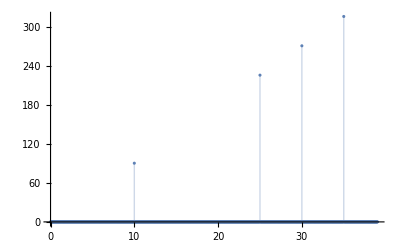

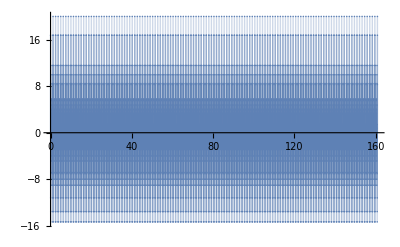

0.01154756760338

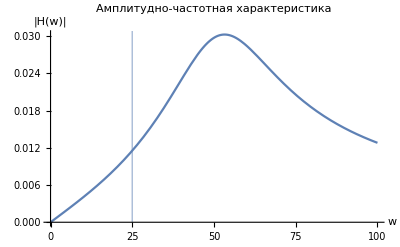

```mathematica
dt=SetPrecision[0.0196349540849362,16];

signalData = SetPrecision[#, 16] & /@ ReadList["C:\\Users\\OLEG\\Desktop\\уник\\фоит\\idz3\\26.txt", Real];Z1[w_]=R1+I w L1;

Z2[w_]=R4+1/(I w C2);

Z3[w_]=1/(I w C1)+R2+I w L2+R3;

Zpar[w_]=Z2[w] Z3[w]/(Z2[w]+Z3[w]);

I1[w_]=Uin/(Z1[w]+Zpar[w]);

Upar[w_]=I1[w] Zpar[w];

IparLeft[w_]=Upar[w]/Z3[w];

Uout[w_]=IparLeft[w]*R2;

H[w_]=Uout[w]/Uin;

N1= Length[signalData];
xValues = Table[dt * (i - 1), {i, 1, N1}];
fourierSignalData = Fourier[signalData];
df = 1 / (dt * N1);

spectrumData = Table[{2π * df * (i - 1), Abs@fourierSignalData[[i]]}, {i, 1, 1000}];
ListPlot[spectrumData, Filling->Axis]
ListPlot[Transpose[{xValues, signalData}], Filling->Axis, PlotRange -> {{0, dt * N1}, Automatic}]

Abs@H[25]


Show[AChH,ListPlot[{{25,0.5}},Filling->Axis]]
```